```mathematica
(*PSOA*)
```

```mathematica
PSO[f_,dim_,popsize_,interval_,generationNum_]:=Module[{},
(*Initialization*)

G=RandomReal[interval,{popsize,dim}];
wstart=0.9;wend=0.4;
c1=c2=1.49618;
v=Table[0,dim];
pBest=G;
x=G;
gBestSolutionVector={};
(*PSOA algorithm*)
For[n=0,n<generationNum,n++,
(*calculate w*)

w=(wstart-(wstart-wend)*n/generationNum)//N;
pBestSolutions=Table[f[pBest[[a]]],{a,popsize}];

(*get gBest from pBest*)

gBest=pBest[[First@Flatten@Position[pBestSolutions,Min@pBestSolutions]]];
gBestSolution=f@gBest;

(*store each generation gBest solution into gBest solution vector for convergence graph*)
AppendTo[gBestSolutionVector,gBestSolution];

(*manipulate individuals*)

For[i=1,i<=popsize,i++,

For[j=1,j<=dim,j++,

(*get v*)
v[[j]]=w*v[[j]]+c1*RandomReal[1]*(pBest[[i]][[j]]-x[[i]][[j]])+c2*RandomReal[1]*(gBest[[j]]-x[[i]][[j]]);
(*limit v less than 20%*interval*)

If[v[[j]]>0.2*(interval[[2]]-interval[[1]]),v[[j]]=0.2*(interval[[2]]-interval[[1]])];
(*update x*)

x[[i]][[j]]=x[[i]][[j]]+v[[j]];

(*limit x inside the interval*)

If[x[[i]][[j]]>interval[[2]],x[[i]][[j]]=interval[[2]],If[x[[i]][[j]]<interval[[1]],x[[i]][[j]]=interval[[1]]]];


];
(*update pBest*)

If[f[x[[i]]]<pBestSolutions[[i]],pBest[[i]]=x[[i]]];

]

];
Return[gBestSolutionVector]
]
```

```mathematica
(*SPHERE FUNCTION*)
sphere[x_]:=Module[
{},Sum[(x[[i]])^2,{i,Length@x}]]
```

```mathematica
(*SUM OF DIFFERENT POWERS FUNCTION*)
```

```mathematica
SDP[x_]:=Module[{l=Length@x},Sum[Abs[x[[i]]]^(i+1),{i,l}]]
```

```mathematica
(*SUM SQUARES FUNCTION*)
```

```mathematica
SS[x_]:=Module[{l=Length@x},Sum[i*(x[[i]]^2),{i,l}]]
```

```mathematica
(*TRID FUNCTION*)
```

```mathematica
Trid[x_]:=Module[{l=Length@x},Sum[(x[[i]]-1)^2,{i,l}]-Sum[x[[i]]*x[[i-1]],{i,2,l}]]
```

```mathematica
(*ROTATED HYPER-ELLIPSOID FUNCTION*)
```

```mathematica
RHE[x_]:=Module[{l=Length@x},Sum[Sum[x[[j]]^2,{j,i}],{i,l}]]
```

```mathematica
(*Convergence graphs*)
```

```mathematica
PSO[sphere,5,10,{-500,500},100]
```

{191514.,191514.,191514.,191514.,191514.,191514.,72616.3,49222.1,49222.1,49222.1,49222.1,49222.1,49222.1,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,12693.9,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6575.63,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,6148.54,4885.21,4885.21,4885.21}

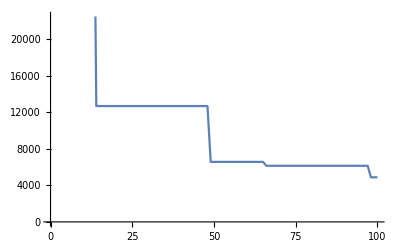

```mathematica
ListLinePlot@gBestSolutionVector
```

```mathematica
PSO[SDP,5,10,{-500,500},100]
```

{5.06937×10^10,5.06937×10^10,5.06937×10^10,4.12488×10^10,2.21159×10^10,2.17366×10^10,2.17366×10^10,1.02266×10^10,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,4.92225×10^9,8.74671×10^8,8.74671×10^8,8.74671×10^8,8.74671×10^8,8.74671×10^8,8.74671×10^8,8.74671×10^8,8.74671×10^8,8.74671×10^8,8.74671×10^8,8.74671×10^8,8.74671×10^8,2.54059×10^8,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6,1.32796×10^6}

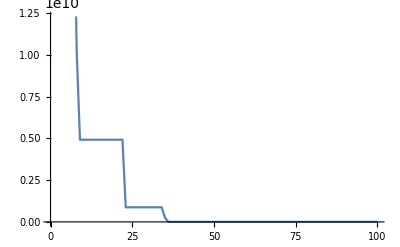

```mathematica
ListLinePlot@gBestSolutionVector
```

```mathematica
PSO[SS,5,10,{-500,500},100]
```

{655777.,463500.,463500.,463500.,285170.,285170.,285170.,285170.,142566.,142566.,142566.,142566.,79912.1,79912.1,68470.8,68470.8,68470.8,68470.8,68470.8,68470.8,68470.8,68470.8,68470.8,38723.9,38723.9,38723.9,38723.9,38723.9,38723.9,38723.9,38723.9,38723.9,38723.9,38723.9,38723.9,38723.9,23597.3,23597.3,23597.3,14031.5,14031.5,14031.5,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,13476.7,5770.58,5770.58,5770.58,5770.58,5770.58,5770.58,5770.58,5770.58,5770.58,1413.42,1413.42,1413.42,1413.42,1413.42,1413.42,1413.42,1413.42,1413.42}

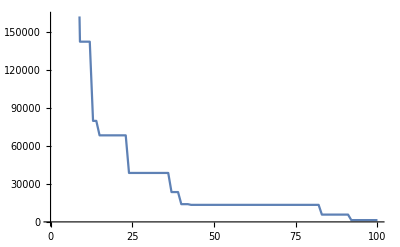

```mathematica
ListLinePlot@gBestSolutionVector
```

```mathematica
PSO[Trid,5,10,{-500,500},100]
```

{309493.,287542.,243429.,243429.,122709.,122709.,122709.,106296.,99932.3,99932.3,99932.3,99932.3,90190.2,90190.2,90190.2,90190.2,90066.9,86375.3,86375.3,86375.3,71941.5,71941.5,59450.9,59450.9,59450.9,59450.9,59450.9,59450.9,48863.3,20270.9,17118.1,15957.3,15957.3,15957.3,15957.3,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,9613.27,7459.33,7459.33,7459.33,7459.33,7459.33,7459.33,7459.33,7459.33,7459.33,7459.33,7459.33,6890.28,6890.28,6890.28,6890.28,6890.28,6890.28,6890.28,6890.28,6890.28,6890.28,6890.28,6890.28,6890.28,6890.28,4483.9,4483.9,4197.2,4197.2,4197.2,4197.2}

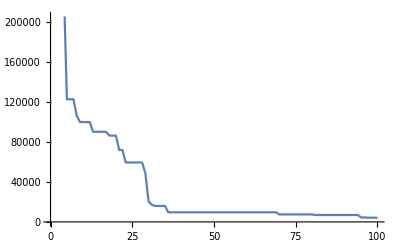

```mathematica
ListLinePlot@gBestSolutionVector
```

```mathematica
PSO[RHE,5,10,{-500,500},100]
```

{467066.,467066.,337719.,105166.,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,95266.7,39593.7,39593.7,39593.7,39593.7,39593.7,39593.7,39593.7,39593.7,39593.7,39593.7,39593.7,39593.7,39593.7,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,17257.1,13886.1,13886.1,13886.1,13886.1,13886.1,13886.1,13886.1,13886.1,13886.1,13886.1,13886.1,13886.1,13886.1,13886.1,6141.75,6141.75,6141.75,6141.75,6141.75,6141.75,6141.75,6141.75,6141.75,6141.75,6141.75,6141.75,6141.75}

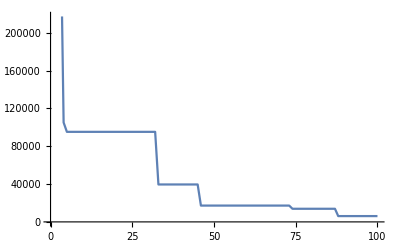

```mathematica
ListLinePlot@gBestSolutionVector
```